```mathematica
Clear["Global`*"]
<<MaTeX`
PathNumber=4;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Codes\\0\\",i==3},{"/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==4}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Figures\\",i==3},{"/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==4}}];
SetDirectory[CodePath[PathNumber]];
v0=2.20;
vE=2.30;
vesc=5.84;
norm=Integrate[v(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vE+vesc}]-Integrate[v(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vesc-vE}];
pdf[v_]=v (Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]-(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2])(1-HeavisideTheta[v-vesc+vE]))/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{cdf[vi],vi},{vi,0,vesc+vE,(vesc+vE)/10^5}]];
vc=3000;
```

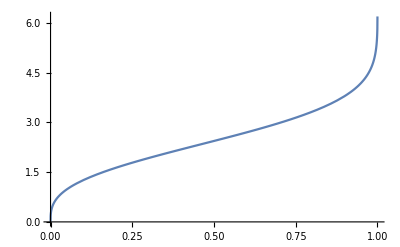

```mathematica
Plot[inverse[x],{x,0,1}]
```

```mathematica
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]/vc},{10^6}];
Export["vi_Erickcek.dat",dis];
```

```mathematica
ss=Import["vi_Erickcek.dat","Data"];
vc=3000;
vI=Table[100vc ss[[i]][[1]],{i,1,2*10^5}];
```

```mathematica
vI=Table[100vc ss[[i]][[1]],{i,1,2*10^5}];
vIhistogram=Histogram[{vI},45,"PDF",ChartStyle->{{Gray},Directive[EdgeForm[]]},Frame->True,ChartLayout->"Overlapped",FrameLabel->{{MaTeX["f(v_i)"],""},{MaTeX["v_i\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},ChartLegends->Placed[SwatchLegend[{MaTeX["Generated"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.8,0.7}]];
vMax=FindRoot[D[pdf[x],x],{x,3}][[1,2]];
lineMax=Line[{{100vMax,0},{100vMax,pdf[vMax]/100}}];
vMean=Mean[vI];
lineMean=Line[{{vMean,0},{vMean,pdf[vMean/100]/100}}];
line=ListPlot[{Table[{100v,pdf[v]/100},{v,0,vesc+vE,1/100}]},Joined->True,PlotStyle->(Directive[#,AbsoluteThickness[3]]&/@{Green}),PerformanceGoal->"Speed",Frame->True,FrameLabel->{{MaTeX["f(v_i)"],""},{MaTeX["v_i\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotLegends->Placed[SwatchLegend[{MaTeX["Actual"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.8,0.7}],Epilog->{Directive[Red,Dashed,AbsoluteThickness[2]],lineMax},Prolog->{Directive[Purple,DotDashed,AbsoluteThickness[1.5]],lineMean}];
p=Show[line,vIhistogram]
Export[FigPath[PathNumber]<>"Maxwellian.pdf",p,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian.pdf

```mathematica
vMean
```

346.63

```mathematica
vMax
```

3.2626

```mathematica
Clear["Global`*"]
<<MaTeX`
PathNumber=4;
CodePath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Codes/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/XQC/Codes/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Codes\\0\\",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/XQC/Codes/",i==4}}];
FigPath[i_]=Piecewise[{{"/home/mahdawi/DAMIC/Figures/",i==1},{"/home/users2/msm550/Desktop/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/",i==2},{"C:\\Users\\shafi\\Desktop\\Dropbox\\Physics\\Research\\H-dibaryon\\DAMIC\\Figures\\",i==3},{"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/",i==4}}];
SetDirectory[CodePath[PathNumber]];
v0=220;
vesc=584;
norm=Integrate[v^2Exp[-(v/v0)^2],{v,0,vesc}];
pdf[v_]=v^2Exp[-(v/v0)^2]/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{N[cdf[vi],665],vi},{vi,0,vesc}]];
vc=300000;
```

```mathematica
vDMHalo=ParallelTable[{ Abs[inverse[RandomVariate[UniformDistribution[]]]]/vc,RandomVariate[UniformDistribution[{-1,1}]]},{10^6}];
Export["vi_g_30.dat",vDMHalo];
```

$Aborted

```mathematica
vDetHalo={39.14,230.5,3.57};
vDMHalo=ParallelTable[Abs[inverse[RandomVariate[UniformDistribution[]]]],{10^6}];
angles=ParallelTable[{RandomVariate[UniformDistribution[{-1,1}]],RandomVariate[UniformDistribution[{0,2 Pi}]]},{10^6}];
vDMHalo3=ParallelTable[{vDMHalo[[i]]Sin[ArcCos[angles[[i,1]]]]Cos[angles[[i,2]]],vDMHalo[[i]]Sin[ArcCos[angles[[i,1]]]]Sin[angles[[i,2]]],vDMHalo[[i]]angles[[i,1]]},{i,10^6}];
```

```mathematica
vDMDetEarth=ParallelTable[{vDMHalo3[[i,1]]-vDetHalo[[1]],vDMHalo3[[i,2]]-vDetHalo[[2]],vDMHalo3[[i,3]]-vDetHalo[[3]]}/vc,{i,10^6}];
Euler[α_,β_,γ_]:={{Cos[α]  Cos[γ]-Cos[β]Sin[α] Sin[γ],-Sin[γ] Cos[α]-Sin[α] Cos[β] Cos[γ],Sin[α] Sin[β]},{ Cos[γ] Sin[α]+Cos[β]Cos[α] Sin[γ],Cos[α] Cos[γ]Cos[β]- Sin[α] Sin[γ],-Cos[α] Sin[β]},{Sin[γ] Sin[β],Sin[β] Cos[γ],Cos[β]}}
rot[l_,b_]:=Euler[Pi(l-90)/180,Pi b/180,0]
RDet=rot[90,60];
RLaunch=rot[71,53.92];
vNorm=ParallelTable[Norm[vDMDetEarth[[i]]],{i,10^6}];
vDMDetS=ParallelTable[{vNorm[[i]],angles[[i,1]],vDMDetEarth[[i,2]]/vNorm[[i]],Take[RLaunch.vDMDetEarth[[i]],{2}][[1]]/vNorm[[i]],Take[RDet.vDMDetEarth[[i]],{2}][[1]]/vNorm[[i]]},{i,10^6}];
```

```mathematica
vDMDetS[[1,1]]vc
```

816.158

```mathematica
vDMDetS=SortBy[vDMDetS,Last];
Export["viE_sortedDet.dat",vDMDetS];
```

```mathematica
a={{1,2,6},{3,4,5},{8,3,5}};
Sort[a,#1[[3]]>#2[[3]]&]
```

{{1,2,6},{8,3,5},{3,4,5}}

```mathematica
vDMDetS=Sort[vDMDetS,#1[[4]]<#2[[4]]&];
Export["viE_sortedLaunch.dat",vDMDetS];
```

```mathematica
vDMDetS=Sort[vDMDetS,#1[[1]]>#2[[1]]&];
Export["viE_sortedNorm.dat",vDMDetS];
```

```mathematica
Euler[α,β,γ].{x,y,z}//MatrixForm
```

(z Sin[α] Sin[β]+y (-Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ])+x (Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ])
-z Cos[α] Sin[β]+x (Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ])+y (Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ])
z Cos[β]+y Cos[γ] Sin[β]+x Sin[β] Sin[γ])

```mathematica
myArcTan[x_,y_]:=Piecewise[{{ArcTan[x,y],y>0 },{2Pi+ArcTan[x,y],y<0 }}]
vDMDetS=ParallelTable[{Norm[vDMDet[[i]]],vDMDet[[i,3]]/Norm[vDMDet[[i]]],myArcTan[vDMDet[[i,1]],vDMDet[[i,2]]]},{i,10^6}];
```

```mathematica
RDet
```

{{0,0,-1},{1,0,0},{0,-1,0}}

```mathematica
Euler[Pi(-90-90)/180,Pi 60/180,0].{0,1,0}
```

{0,-1/2,(√3)/2}

```mathematica
RotationMatrix[{{0,1,0},{1/4,Sqrt[3]/4,Sqrt[3]/2}}].{0,1,0}
```

{1/4,(√3)/4,(√3)/2}

```mathematica
RotationMatrix[{{0,1,0},{0,1/2,Sqrt[3]/2}}].{0,1,0}
```

{0,1/2,(√3)/2}

```mathematica
rot1[l_,b_]:=RotationMatrix[{{0,1,0},{Sin[(90-b)  Pi/180]Cos[l Pi/180],Sin[(90-b)  Pi/180]Sin[l Pi/180],Cos[(90-b) Pi/180]}}]
rot1[90,60]
```

{{1,0,0},{0,1/2,-(√3)/2},{0,(√3)/2,1/2}}

```mathematica
Euler[α_,β_,γ_]:={{Cos[α]  Cos[γ]-Cos[β]Sin[α] Sin[γ],-Sin[γ] Cos[α]-Sin[α] Cos[β] Cos[γ],Sin[α] Sin[β]},{ Cos[γ] Sin[α]+Cos[β]Cos[α] Sin[γ],Cos[α] Cos[γ]Cos[β]- Sin[α] Sin[γ],-Cos[α] Sin[β]},{Sin[γ] Sin[β],Sin[β] Cos[γ],Cos[β]}}
rot[l_,b_]:=Euler[Pi(l-90)/180,Pi b/180,0]
rot1[90,60]
```

{{1,0,0},{0,1/2,-(√3)/2},{0,(√3)/2,1/2}}

```mathematica
rot1[l_,b_]:={Sin[b Pi/180]Cos[l Pi/180],Sin[b Pi/180]Sin[l Pi/180],Cos[b Pi/180]}
rot1[90,60]
```

{0,(√3)/2,1/2}

```mathematica
vDMDetS=Import["viE_sortedNorm.dat","Data"];
```

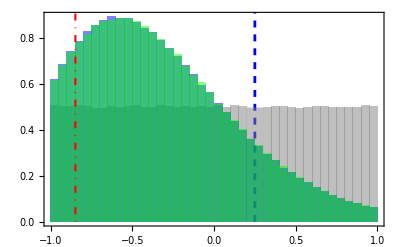

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/Zenith_angle_dis.pdf

```mathematica
LaunchBound=Line[{{.25,0},{.25,.94}}];
DetBound=Line[{{-.848,0},{-.848,.94}}];
cosdis=Histogram[Table[vDMDetS[[i,j]],{j,{2,4,5}},{i,10^6}],40,"PDF",ChartStyle->{{Gray,Blue,Green},Directive[EdgeForm[]]},Frame->True,ChartLayout->"Overlapped",FrameLabel->{{MaTeX["Probability\\;Distribution"],""},{MaTeX["cos\\,\\theta"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},ChartLegends->Placed[SwatchLegend[{MaTeX["Galactic\\;frame"],MaTeX["XQC\\;launch"],MaTeX["XQC\\;detection"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.82,0.78}],Prolog->{Directive[Blue,Dashed,AbsoluteThickness[2]],LaunchBound},Epilog->{Directive[Red,DotDashed,AbsoluteThickness[1.5]],DetBound}]
Export[FigPath[PathNumber]<>"Zenith_angle_dis.pdf",cosdis,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
Body=Graphics[Text[Rotate[MaTeX["Body\\;shielding"],Pi/2],{-.76,0.23},Background-> White]];
Earth=Graphics[Text[Rotate[MaTeX["Earth\\;shielding"],Pi/2],{.18,0.24},Background-> White]];
cosdis2=Show[cosdis,Body,Earth]
Export[FigPath[PathNumber]<>"Zenith_angle_dis(v2).pdf",cosdis2,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

-Graphics-

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/Zenith_angle_dis(v2).pdf

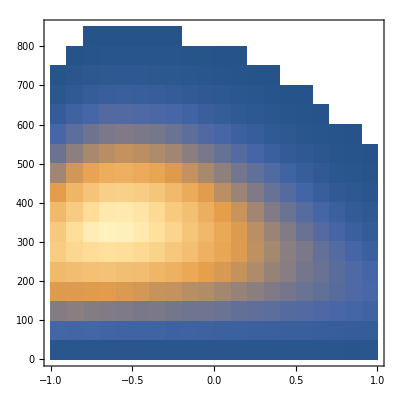

```mathematica
DensityHistogram[Table[{vDMDetS[[i,4]],vc vDMDetS[[i,1]]},{i,10^6}],Frame->True,FrameLabel->{{MaTeX["v\\,(km/s)"],""},{MaTeX["cos\\,\\theta"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0}]
```

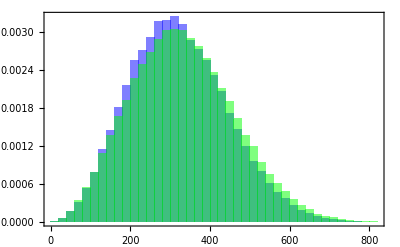

```mathematica
vI2=Table[300000 vDMDet[[i,1]],{i,1,2*10^5}];
vI1=Table[300000 E32[[i,1]],{i,1,102758}];
vIhistogram2=Histogram[{vI1,vI2},45,"PDF",ChartStyle->{{Blue,Green},Directive[EdgeForm[]]},Frame->True,ChartLayout->"Overlapped",FrameLabel->{{MaTeX["f(v_i)"],""},{MaTeX["v_i\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},ChartLegends->Placed[SwatchLegend[{MaTeX["My\\; method"],MaTeX["Your\\; method"]},LabelStyle->{GrayLevel[0.1],FontFamily-> "CMU Serif",10}],{0.8,0.7}]]
```

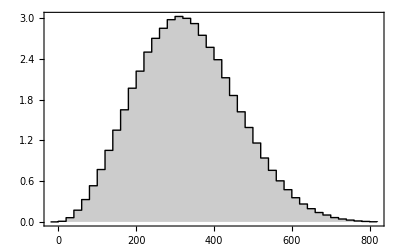

/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian_Erickcek.pdf

```mathematica
vDMDet=vDMDetS;
vI2=Table[300000 vDMDet[[i]][[1]],{i,1,10^6}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Black],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0}]
Export[FigPath[PathNumber]<>"Maxwellian_Erickcek.pdf",vIhistogram,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
"/Users/Shafi/Google Drive/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian_Erickcek.pdf"
```

```mathematica
vDMg=Import["vi_g.dat","Data"];
vI2=Table[300000 vDMg[[i]][[1]],{i,1,2*10^5}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram2=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Orange],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotRange->{{0,850},{0,4}}];
vDMg=Import["vi_g_30.dat","Data"];
vI2=Table[300000 vDMg[[i]][[1]],{i,1,2*10^5}];
<<MaTeX`
hd=HistogramList[vI2,45];
histPlotAdjust[histList_]:=Module[{bins,counts},With[{binLength=histList[[1,2]]-First@histList[[1]]},bins={First@histList[[1]]-binLength}~Join~histList[[1]];
counts={0}~Join~(1000histList[[2]]/Length[vI2]/binLength)~Join~{0};
{bins,counts}]]
hd=histPlotAdjust[hd];
vIhistogram3=ListLinePlot[Transpose[hd],InterpolationOrder->0,PlotStyle->Directive[Thick,Blue],PlotStyle->Thick,Filling->Axis,Frame->True,FrameLabel->{{MaTeX["f(v)\\times10^3"],""},{MaTeX["v\\;(km/s)"],""}},BaseStyle->{FontFamily->"CMU Serif",FontSize->10},AxesOrigin-> {0,0},PlotRange->{{0,850},{0,28}}];
```

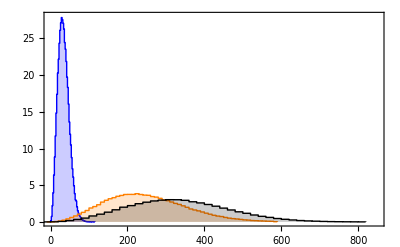

/Users/Shafi/Dropbox/Physics/Research/H-dibaryon/DAMIC/Figures/Maxwellian_Extreme.pdf

```mathematica
vEx=Show[vIhistogram3,vIhistogram2,vIhistogram]
Export[FigPath[PathNumber]<>"Maxwellian_Extreme.pdf",vEx,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

```mathematica
vI2=Table[300000 vDMg[[i]][[1]],{i,1,10^6}];
```

```mathematica
Max[vI2]
```

121.821

```mathematica
vDMDetS=Import["viE_sortedLaunch.dat","Data"];
count=BinCounts[vDMDetS[[1;;10^6,1]],5*10^-5];
```

```mathematica
f=Interpolation[Join[{{0,0}},Table[{5i 10^-5,count[[i]]/10^6},{i,1,Length[count]}]]]
```

11
InterpolatingFunction[{{0, ----}}, <>]
                           4000

```mathematica
norm=NIntegrate[v f[v],{v,0,816/300000}];
cdfv[vi_]:=NIntegrate[v f[v],{v,0,vi}]/norm;
inverse=Interpolation[Table[{cdfv[vi],vi},{vi,0,816/300000,10^-5}]];
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]},{10^6}];
```

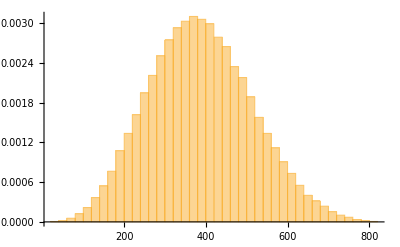

```mathematica
vI=Table[vc dis[[i]][[1]],{i,1,2*10^5}];
vIhistogram=Histogram[{vI},45,"PDF"]
```

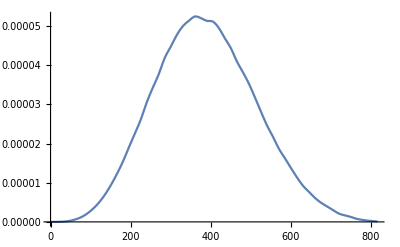

```mathematica
line=ListPlot[{Table[{vc v, v f[v]},{v,0,816/300000,10^-5}]},Joined->True]
```

```mathematica
norm=Integrate[v^2(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vE+vesc}]-Integrate[v^2(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2]),{v,0,vesc-vE}];
pdf[v_]=v ^2(Exp[-((v-vE)/v0)^2]-Exp[-(vesc/v0)^2]-(Exp[-((v+vE)/v0)^2]-Exp[-(vesc/v0)^2])(1-HeavisideTheta[v-vesc+vE]))/norm;
cdf[vi_]=Integrate[pdf[v],{v,0,vi}];
inverse=Interpolation[Table[{cdf[vi],vi},{vi,0,vesc+vE,(vesc+vE)/10^5}]];
vc=3000;
```

Interpolation::inddp: The point 1.32718×10^-16 in dimension 1 is duplicated.

```mathematica
dis=ParallelTable[{Abs[inverse[RandomVariate[UniformDistribution[]]]]},{10^6}];
```

Interpolation::inddp: The point 1.32718×10^-16 in dimension 1 is duplicated.

```mathematica
vI2=Table[100vc dis[[i]][[1]],{i,1,2*10^5}];
vIhistogram2=Histogram[{vI2},45,"PDF"]
```